# Watergate: An Accessible Computational Model for Flooding Analysis

240 million people are affected by floods each year, reflecting the urgent need for accessible flood prediction and detection. WaterGate is a computational model that uses geographic elevation data and the rational method to predict flooding patterns , generating an interactive 3D model for user accessibility. Computational hydrology applies numerical methods, machine learning algorithms, and computational simulations to understand, predict, and manage water resources - including floods. Our project employs computational hydrology by analyzing the structure of river tributaries in 2D through polygon clustering, satellite imaging, and various cleaning protocols. We developed respective tributary tree graphs, morphological graphs, and nodes to create a comprehensive tree and 3D model. Afterward, we examine the morphology of flood plains in 3D space, implementing the rational method (Q = C iA) framework with curated relief plots to predict, model, and visualize flooding elevation. Then, we constructed our stream order analysis, waterline delineation, and statistical analysis to validate our date. Lastly, we modeled different river systems and developed further extensions to increase the applicability of WaterGate to communities around the world.

## Merit for Analyzing Properties of River Tributaries

Current methods of analyzing river tributaries are limited to "notable" rivers and streams.  As rivers are not GeoEntities, river data extraction is extremely limited, and the database for "notable" rivers do not identify tributary points, connectedness, nor stream order identification. This section focuses on the methodology of a novel extraction of river polygons, the labeling of tributary "split-points", the identification of these split points, the creation of tree graphs & morphological graphs, and the establishment and implementation of stream order identification for rivers and their tributaries.

## Isolating Rivers from Maps

This first step of this section is to find a way to isolate rivers from a Map; we can do this through polygon clusters and color recognition. VectorMinimal allows us to convert individual components on the map into manipulable polygons. GeoBoundingBox gives the coordinates of the bounding rectangle enclosing the extracted polygon. GeoGraphics simply gives the map of all said polygons in the region. 

Let's take Paris, France; we'll name the variable parisMap:

```mathematica
parisMapData = GeoGraphics[GeoBoundingBox[Entity["City",{"Paris","IleDeFrance","France"}]], GeoBackground -> "VectorMinimal"]

parisMap = ImageResize[parisMapData,500]
```

-Graphics-

Then we can take the color of the river on parisMap, RGBColor[0.6, 0.807843137254902, 1.0] { RGBColor[0.6, 0.807843137254902, 1.]}, and extract all polygons that match the criteria of that color. Specifically, we will employ Cases and Select to parse through the objects with {RGBColor[0.6, 0.807843137254902, 1.]} color with the condition Not @ * FreeQ[Polygon] to iterate through parisMap until there are no more "Free" {RGBColor[0.6, 0.807843137254902, 1.]}polygons.

Let' s visualize river extraction in Paris through riverParis :

```mathematica
riverParis=Graphics[Select[Cases[parisMapData,{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]]
```

-Graphics-

However, this function extracts all the blue polygons in the map --- this includes the extraneous water structures separate from the main river and its tributaries. We can fix this through cleaning functions like Dilation (to enlarge all components to connect river polygons), DeleteSmallComponents (to delete all the unconnected, small components), and Thinning (to return the river back to a manageable size).

Applied to parisRiver, we get parisOutline:

```mathematica
parisOutline =
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[parisMapData,water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]
```

-Graphics-

Using parisOutline, we can now move on to creating morphological graphs and tree graphs.

## Creating Morphological Graphs and Tree Graphs

We can apply MorphologicalGraph to parisOutline to give an undirected graph that represents the connectivity of the morphological branch points and endpoints.

Here is MorphologicalGraph applied to parisOutline to get parisMorphologicalGraph:

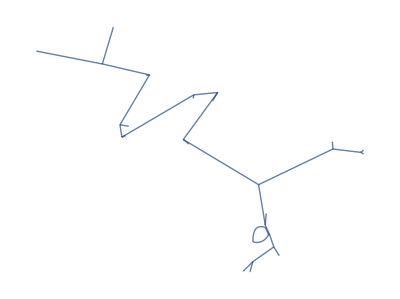

```mathematica
parisMorphologicalGraph=MorphologicalGraph[parisOutline]
```

There are a few major flaws in the parisMorphologicalGraph, however. To overcome this limitation and make the morphological graph acyclic, we can employ the TransitiveReductionGraph function. The TransitiveReductionGraph function works by iteratively eliminating edges that contribute to cycles while preserving the graph's reachability properties; it identifies and removes edges that are transitively implied by other edges in the graph, effectively reducing the number of edges and transforming cyclic components into acyclic ones.

Here it is being applied to parisMorphologicalGraph to get parisReduction3DGraph:

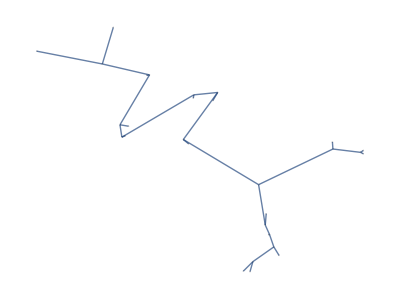

```mathematica
parisReduction3DGraph=TransitiveReductionGraph[parisMorphologicalGraph]
```

Afterwards, we can apply the function GraphTree to convert the morphological graph into a tree graph (this subsequent step allows us to convert morphological graphs into tree graphs while specifying the desired nodes).

Applied to parisReduction3DGraph, we get parisTreeGraph:

```mathematica
parisTreeGraph=GraphTree[TransitiveReductionGraph[parisMorphologicalGraph]]
```

-Graphics-

Now that we have trees, we can find stream splits. Let's see how we can tackle this problem.

## Finding Stream Splits on Morphological Graphs

Finding stream splits through morphological graphs can easily be done using MorphologicalBranchPoints and various data cleaning mechanism. First, we extract the river polygons (this time using pattern matching as it reduces the time complexity); next we Binarize the image and subject it to ColorNegate to turn the river white and the background black. Afterwards, we apply the Dilation function to connect all the river polygons together and use the function DeleteSmallComponents to remove extraneous water sources.  We apply Thinning to return the river to the original size before using the function MorphologicalBranchPoints to point out the pixels that form river splits. Lastly, we dilate the points and make them into circles using Dilatation (once more) and DiskMatrix[5].

Here is an example from Paris once more, let’s call this function branchIdentification:

```mathematica
branchIdentification =
Dilation[
MorphologicalBranchPoints[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[parisMapData,water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]],DiskMatrix[5]]
```

-Graphics-

We successfully found the branches in which the river breaks off. Let's clean up branchIdentification using ColorNegate, ColorReplace, and RemoveBackground. These functions make the branch points more noticeable when plotted in relation with riverParis.

Applied to branchIdenitification, we get branchPoints:

```mathematica
branchPoints =RemoveBackground[ColorReplace[ColorNegate[branchIdentification],Black->Red]]
```

-Graphics-

The final step is to match the points with the river polygons in riverParis (using the same extraction methods as detailed above). Using ImageCompose, we are able to overlay the points with the river tributary splits.

Applied to riverParis and branchPoints, we get layoverImage:

```mathematica
riverParis = Graphics[Select[Cases[parisMapData,{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]];
layoverImage = ImageCompose[riverParis,branchPoints]
```

-Graphics-

Now let's try to map the river polygons with their tributary points on a geographic map and generalize it for all locations.

## Mapping River Branches on Maps

Although the process for evaluating polygons on maps is known, extracting the polygons across a multitude of different maps (with different coloring schemes) is not trivial. Therefore, we first define variables that extract raw data from the map and stores them for them to be manipulated later. We used the functions Nearest and ColorReplace to make the association from the river's blue to our desired blue. 

GeoToGraphicsLayer helps with the syntax of the extraction of graphics layers from a map using functions like Flatten and Cases. The rest of the riverBranchMap pure anonymous function is written so that the code can be applied to other river systems; x_, y_, and z_ variables indicate the city, state/province, and country, respectively, and the f_ variable changes the GeoRange the map takes in. The process involves the same polygon extraction and cleaning protocols detailed above (for both the red nodes along the river tributary splits and the river tributaries themselves) and alignment onto the map.

Here it is, applied to Paris:

```mathematica
GeoToGraphicsLayers[geo_GeoGraphics]:=
Flatten/@GroupBy[
Cases[
geo,
{Directive[{___,color_RGBColor,___}],graphics_List}:>{color,graphics},
Infinity],
First]

parisGeo=GeoGraphics[GeoBoundingBox[Entity["City",{"Paris","IleDeFrance","France"}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[20, "Miles"],GeoRangePadding->None];
parisRawLayers=GeoToGraphicsLayers[parisGeo];
waterColor=Nearest[Keys[parisRawLayers],Blue][[1]];

riverBranchMap[{"Paris","IleDeFrance","France"}, 10]

riverBranchMap[{x_,y_,z_},f_]:=
Graphics[ImageCompose[ImageCompose[Graphics[Values[GeoToGraphicsLayers[GeoGraphics[GeoToGraphicsLayers[Entity["City",{x,y,z}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[f,"Miles"],GeoRangePadding->None]]]],RemoveBackground[ColorReplace[Graphics[Lookup[GeoToGraphicsLayers[GeoGraphics[GeoBoundingBox[Entity["City",{x,y,z}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[f,"Miles"],GeoRangePadding->None]],Nearest[Keys[GeoToGraphicsLayers[GeoGraphics[GeoBoundingBox[Entity["City",{x,y,z}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[f,"Miles"],GeoRangePadding->None]]
],Blue][[1]]]],waterColor->Darker[waterColor,.3]]],Center,Center,{1,.4,1}],ColorReplace[RemoveBackground[ColorNegate[Dilation[MorphologicalBranchPoints[Thinning[Dilation[DeleteSmallComponents[ColorNegate[Binarize[Graphics[Lookup[GeoToGraphicsLayers[GeoGraphics[GeoBoundingBox[Entity["City",{x,y,z}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[f,"Miles"],GeoRangePadding->None]],Nearest[Keys[GeoToGraphicsLayers[GeoGraphics[GeoBoundingBox[Entity["City",{x,y,z}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[f,"Miles"],GeoRangePadding->None]]
],Blue][[1]]]]]]],2]]],DiskMatrix[5]]]],Black->Red]],ImageSize->Large]
-Graphics-
```

Now that we have generalized the stream labeling and creation process, let's move on to the applications of this to simple and complex rivers.

## Application to Simple River Systems

Application of this code to simple river systems can present us with overlooked overcomplexity. Tributaries may be over counted, small bodies of water may be presented as a multiple tributary, and tree graphs may be inaccurate. Note that this example was created in a pure anonymous function for the purpose that this code can be applied to other locations.

Here is an example from Jackson, Mississippi, with everything analyzed, evaluated, extracted, mapped, and displayed with the same functions shown above:

```mathematica
mapView[{"Jackson","Mississippi","UnitedStates"}];

mapView[{x2_,y2_,z2_}]:=GeoGraphics[GeoBoundingBox[Entity["City",{x2,y2,z2}]],GeoBackground->"VectorMinimal"];
```

Immediately, we see small amount of tributaries and identify one main river (the Pearl River).

Let’s separate the river polygons (polygonComponents) using Select and Cases:

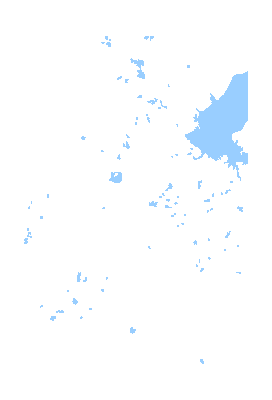

```mathematica
polygonComponents[{"Jackson","Mississippi","UnitedStates"}]

polygonComponents[{x3_,y3_,z3_}]:=Graphics[Select[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x3,y3,z3}]],GeoBackground->"VectorMinimal"],{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]]
```

Then, we'll apply Binarize through the polygonBinarization function to polygonComponents to prepare it for cleaning:

```mathematica
polygonBinarization[{"Jackson","Mississippi","UnitedStates"}]

polygonBinarization[{x4_,y4_,z4_}]:=ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x4,y4,z4}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]]
```

-Graphics-

After, we'll apply Dilation, DeleteSmallComponents, and Thinning through the polygonCleaning function to clean all unconnected, small components:

```mathematica
polygonCleaning[{"Jackson","Mississippi","UnitedStates"}]

polygonCleaning[{x5_,y5_,z5_}]:=Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x5,y5,z5}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]
```

-Graphics-

We'll turn the image into a morphological graph using the threeDFullfunction through MorphologicalGraph and Graph3D:

```mathematica
threeDFullFunction[{"Jackson","Mississippi","UnitedStates"}]

threeDFullFunction[{x6_,y6_,z6_}]:=
Graph3D[
MorphologicalGraph[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x6,y6,z6}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]]]
```

-Graphics-

We'll separate the cyclic components using the threeDReducedFunction through TransitiveReductionGraph:

```mathematica
threeDReducedFunction[{"Jackson","Mississippi","UnitedStates"}]

threeDReducedFunction[{x7_,y7_,z7_}]:=
Graph3D[
TransitiveReductionGraph[
MorphologicalGraph[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x7,y7,z7}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]]]]
```

-Graphics-

Lastly, we'll create the tree graph using treeFunction and specifically GraphTree:

```mathematica
treeFunction[{"Jackson","Mississippi","UnitedStates"}]

treeFunction[{x8_,y8_,z8_}]:=
GraphTree[
TransitiveReductionGraph[
MorphologicalGraph[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x8,y8,z8}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]]]]
```

-Graphics-

Some common flaws with small river systems is that minute tributaries may be counted towards the total calculation of river leaves and large bodies of water may be separated into multiple tributaries. Let's investigate complex river systems now.

## Application to Complex River Systems

Application of this code to more complex river systems may present even more challenges. Tributaries may be uncounted, large bodies of water may be presented as a single tributary, and tree graphs may be inaccurate. Note that this example was created in a pure anonymous function for the purpose that this code can be applied to other locations.

Here is an example from Anchorage, Alaska, with everything analyzed, evaluated, extracted, mapped, and displayed with the same functions shown above:

```mathematica
mapView[{"Anchorage","Alaska","UnitedStates"}];

mapView[{x9_,y9_,z9_}]:=GeoGraphics[GeoBoundingBox[Entity["City",{x9,y9,z9}]],GeoBackground->"VectorMinimal"];
```

Immediately, we see an influx of connected and separate bodies of water with varying tributary sizes.

Let’s separate the river polygons (polygonComponents) using Select and Cases:

```mathematica
polygonComponents[{"Anchorage","Alaska","UnitedStates"}]

polygonComponents[{x10_,y10_,z10_}]:=Graphics[Select[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x10,y10,z10}]],GeoBackground->"VectorMinimal"],{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]]
```

-Graphics-

Then, we'll apply Binarize through the polygonBinarization function to polygonComponents to prepare it for cleaning:

```mathematica
polygonBinarization[{"Anchorage","Alaska","UnitedStates"}]

polygonBinarization[{x11_,y11_,z11_}]:=ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x11,y11,z11}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]]
```

-Graphics-

After, we'll apply Dilation, DeleteSmallComponents, and Thinning through the polygonCleaning function to clean all unconnected, small components:

```mathematica
polygonCleaning[{"Anchorage","Alaska","UnitedStates"}]

polygonCleaning[{x12_,y12_,z12_}]:=Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x12,y12,z12}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]
```

-Graphics-

We'll turn the image into a morphological graph using the threeDFullfunction through MorphologicalGraph and Graph3D:

```mathematica
threeDFullFunction[{"Anchorage","Alaska","UnitedStates"}]

threeDFullFunction[{x13_,y13_,z13_}]:=
Graph3D[
MorphologicalGraph[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x13,y13,z13}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]]]
```

-Graphics-

We'll separate the cyclic components using the threeDReducedFunction through TransitiveReductionGraph:

```mathematica
threeDReducedFunction[{"Anchorage","Alaska","UnitedStates"}]

threeDReducedFunction[{x14_,y14_,z14_}]:=
Graph3D[
TransitiveReductionGraph[
MorphologicalGraph[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x14,y14,z14}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]]]]
```

-Graphics-

Lastly, we'll create the tree graph using treeFunction and specifically GraphTree:

```mathematica
treeFunction[{"Anchorage","Alaska","UnitedStates"}]

treeFunction[{x15_,y15_,z15_}]:=
GraphTree[
TransitiveReductionGraph[
MorphologicalGraph[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[GeoGraphics[GeoBoundingBox[Entity["City",{x15,y15,z15}]],GeoBackground->"VectorMinimal"],water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]]]]
```

-Graphics-

We have seen that the code works for both simple cases and complex cases for all types of river systems; we also see that it is able to generate components for both types of rivers. Now, we'll move on to the second part of my project: terrain-based flood analysis.

## Merit for Analyzing Properties of Terrains in Relation to Floods

Currently, there are no built-in functions that can be used to predict flood plains nor taken into account the elevation data when modeling water elevation increase. There are also minimal datasets that record the flooded amount and areas flooded, given the rainfall amount. This section focuses on the methodology of extracting terrain from satellite imaging, mapping it 3D using GeoElevation, extracting relief plot information, calculating stream elevation rise using Q = CiA, and plotting population density.

## 2-D Satellite Mapping onto 3-D Model

The first step of this section is to find a way to take satellite imagery of a geographic location using GeoImage; afterwards, we will extract the river basin using imaging processing (using Color Matching once more) and layer both the satellite image and the river (using ImageCompose) to create a texture that could be mapped onto ListPlot3D to create a chunk of the specified geographic location.

Let’s see an example in Juneau, Alaska, we name it satelliteImage:

```mathematica
satelliteImage =GeoImage[Entity["City",{"Juneau","Alaska","UnitedStates"}],GeoRange->Quantity[10,"Miles"]];
```

Afterwards, we can extract the river information from a street map through GeoImage. Then, we can clean the data using ColorNegate, Binarize, and ImageRecolor. ColorNegate and Binarize makes its so that only the river component of satelliteImage is present. ImageRecolor recolors the black (from ColorNegate) into a more desirable blue color for the river. StreeMapNoLabels takes away the labels from the street map to foster a more fluid  transition from map to river image.

Here are these functions applied, resulting in riverImage:

```mathematica
riverImage =ImageRecolor[Binarize[ColorNegate[GeoImage[Entity["City",{"Juneau","Alaska","UnitedStates"}],"StreetMapNoLabels",GeoRange->Quantity[10,"Miles"]]]],{White->RGBColor[0,0,Rational[2,3],0.5],Black->RGBColor[0.5,0.5,0.5,0]}]
```

-Graphics-

Then, we will overlay satelliteImage and riverImage through the ImageCompose function.

Applied on Juneau we get fullSatelliteImage:

```mathematica
fullSatelliteImage = ImageCompose[satelliteImage,riverImage]
```

Finally, we can set the overlay as a texture scope and create a ListPlot3D for the entire satellite image. 

And, Juneau will look something like this:

```mathematica
ListPlot3D[GeoElevationData[Entity["City",{"Juneau","Alaska","UnitedStates"}], GeoRange->Quantity[10, "Miles"]],MeshFunctions->{#3&}, PlotRange->All,PlotStyle->Texture[ImageRotate[fullSatelliteImage, 3Pi/2]], Filling-> Bottom, FillingStyle->Opacity[1], ImageSize->1000]
```

-Graphics-

Now that we have basic satellite imaging, we can move into more complex satellite imaging with relief plots and the rational method.

## Relief Plot for Flood Plain

A relief plot can be especially helpful to model the flood plain of a particular area. We can apply the function MinMax to find the range of the manipulate, ColorReplace to fill in the "flooded" space with RGBColor[0.6, 0.807843137254902, 1.0] { RGBColor[0.6, 0.807843137254902, 1.]}, and Dynamic@ to synchronously reflect the changes made.

Here it is in Juneau, we’ll call it juneauData, juneauLevelPlot, and juneauReliefPlot respectively:

```mathematica
juneauData=GeoElevationData[Entity["City",{"Juneau", "Alaska", "UnitedStates"}],GeoRange->Quantity[20,"Miles"],GeoProjection->Automatic,UnitSystem->"Imperial"];
{mi,ma}=QuantityMagnitude[MinMax[juneauData]];
juneauLevelPlot=Manipulate[ReliefPlot[juneauData,PlotRange->{rainfall,ma}],{rainfall,mi,ma},SynchronousUpdating->True,SynchronousInitialization->True,LocalizeVariables->False]
juneauReliefPlot = Dynamic@With[{level=rainfall},ColorReplace[ReliefPlot[juneauData,PlotRange->{level,ma}],White->Directive[RGBColor[0.6,0.807843137254902,1.],Opacity[0.2]]]];
```

-Graphics-

We can also plot this data if we set the manipulate to an image. 

Here is an example of Juneau's flood plain and relief plot using Setting; we'll name it reliefTrue:

```mathematica
juneauReliefTrue=Setting[juneauReliefPlot]
```

-Graphics-

Finally, we can set the overlay as a texture scope and create a ListPlot3D for the entire relief plot. 

And, Juneau's flood plain will look something like this:

```mathematica
ListPlot3D[GeoElevationData[Entity["City",{"Juneau", "Alaska", "UnitedStates"}], GeoRange->Quantity[10, "Miles"]],MeshFunctions->{#3&}, PlotRange ->All,PlotStyle->Texture[juneauReliefTrue],Filling-> Bottom, FillingStyle->Opacity[1], ImageSize->1250]
```

-Graphics-

Now that we have knowledge on both basic satellite imaging and satellite imaging with relief plots, we can focus on the rational method.

## Rational Method (Q = CiA) Introduction and Usage

The rational method  is used for determining peak discharges; this method is traditionally used to size storm sewers, channels, and other stormwater structures.

The rational method formula is expressed as Q = CiA where: Q = Peak rate of runoff in cubic feet per second; C = Runoff coefficient, an empirical coefficient representing a relationship between rainfall and runoff; i = Average intensity of rainfall in inches per hour for the time of concentration for a selected frequency of occurrence or return period; A = The watershed area in acre. In this section, we will be calculating each of these variables and parameterizing them for any geographic location.

## Q = CiA (C Calculation)

As C is the runoff coefficient, we conducted a weighted average for all the colors present in the map with their coefficients taken from this table:

-Graphics-

As colors from different regions may differ, we have to build an algorithm that converts the closest color to the colors in our key. Using Nearest and ReplaceAll we are able to associate the correct colors with the correct weights. Afterwards we can see the color coverage of all the regions in the map using "Color" and "Coverage" as the option for the DominantColors function and apply the weight to get our final C value.

Here is an example from Juneau, we’ll name it juneauGeo:

```mathematica
juneauGeo=GeoGraphics[GeoBoundingBox[Entity["City",{"Juneau","Alaska","UnitedStates"}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[20, "Miles"],GeoRangePadding->None];juneauDominantColorsCity=DominantColors[juneauGeo,5];
juneauCanonicalColorValueMap={RGBColor[0.9485373223930705, 0.9487508349546278, 0.9489485072522973, 1.]->0.8,RGBColor[0.6313832857283339, 0.7646670368551112, 0.498099288620747, 1.]->0.25,RGBColor[0.9997462475099389, 0.8507363495836935, 0.3998398617073094, 1.]->0.85,RGBColor[0.9993720538256167, 0.7492570006072168, 0.003109412403643569, 1.]->0.65,RGBColor[0.2960132375888991, 0.2960131125158366, 0.2960131444661215, 1.]->0.8,RGBColor[0.6000193760698551, 0.8071089170241192, 0.998613272437677, 1.]->0.01,RGBColor[0.09982824341023538, 0.3304382676154282, 0.6514924833695483, 1.]->0.01, RGBColor[0.6540282036622517, 0.6540488377301875, 0.6540691378617204, 1.] ->0.75};
juneauCleanupRules=MapThread[Rule,{Flatten@Nearest[Keys@juneauCanonicalColorValueMap,juneauDominantColorsCity],juneauDominantColorsCity}];
juneauCityValueMap=juneauCanonicalColorValueMap/.juneauCleanupRules;
juneauCityColorCoverage=DominantColors[juneauGeo,5,{"Color","Coverage"}];
Transpose[juneauCityColorCoverage/.juneauCityValueMap];
juneauCityWeightedByColor=WeightedData@@Transpose[juneauCityColorCoverage/.juneauCityValueMap];

juneauPermeability=Mean[juneauCityWeightedByColor]
```

0.633755

## Q = CiA (i Calculation)

i is the intensity of the rainfall. Previous literature found that the intensity of rainfall for flash floods is usually around 4-6 inches; by taking the rainfall data using WeatherData for the past 20+ years, we are able to find an average annual rainfall measured in centimeters (which we converted to inches by dividing by 2.54). Next we mapped the intensity of rainfall (if it were to flood) and set it proportional to how high the annual rainfall is using a Which function.

Here is it being applied to Juneau and name it intensityCalibrated:

```mathematica
juneauIntensity = Mean[WeatherData[Entity["City",{"Juneau","Alaska","UnitedStates"}],"TotalPrecipitation",{{2000,1,1},{2022,12,31}, "Year"}]]/2.54;

juneauIntensityCalibrated = Which[0<juneauIntensity<5,4.1 ,5<juneauIntensity<10,4.2 ,10<juneauIntensity<15,4.3 ,15<juneauIntensity<20,4.4, 20<juneauIntensity<25,4.5 ,25<juneauIntensity<30,4.6 ,130<juneauIntensity<35,4.7 ,35<juneauIntensity<40,4.8 ,40<juneauIntensity<45,4.9 ,45<juneauIntensity<50,5.0 ,50<juneauIntensity<55,5.1 ,55<juneauIntensity<60,5.2 , 60<juneauIntensity<65,5.3 ,65<juneauIntensity<70,5.4 ,70<juneauIntensity<75,5.5 ,75<juneauIntensity<80,5.6 , 80<juneauIntensity<85,5.7 ,85<juneauIntensity<90,5.8 , 90<juneauIntensity<95,5.9 ,95<juneauIntensity<100, 6.0]
```

4.9

## Q = CiA (A Calculation)

A is the area of the flood plain in acres; current data was in miles. To convert miles to acres, we have to square the region boundaries (the return result will be in square miles), then multiply by 640.

Represented in Juneau, named acres:

```mathematica
juneauAcres = 20^2*640
```

256000

## Q = CiA (Q Calculation) & River Runoff Calculation

Multiplying the permeability, intensity, and acres values, we are able to derive the peakRunoff rate for Juneau, Alaska (or the Q value):

```mathematica
juneauPeakRunoff = juneauPermeability*juneauIntensityCalibrated*juneauAcres
```

794982.

Firstly, we want to multiply the peakRunoff calculation (Q) by the inverse to model the factor in which the river will increase with respect to time. Then, we'll convert 400 square mile to 11,151,360,000 square feet and multiply  3600 to convert seconds to hours (the original measurement of Q is cubic feet/second). This measurement will give us the units measurement of feet/hour, in which we can manipulate the amount of hours the flood occurs to give the totalRiverIncrease.

```mathematica
juneauTotalRiverIncrease= riverRunoffCalculator[{"Juneau","Alaska","UnitedStates"},750]
riverRunoffCalculator[{x_,y_,z_}, h_]:=
(juneauPeakRunoff/Part[Part[#,2]&/@Select[DominantColors[GeoGraphics[GeoBoundingBox[Entity["City",{x,y,z}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[20, "Miles"],GeoRangePadding->None],5,{"Color","Coverage"}],ColorDistance[RGBColor[0.5998694708331431, 0.8076220271551392, 0.9996520209699861, 1.],#[[1]]]<0.1&],1])/11151360000*3600*h
```

1422.29

## Relief Calculation Integration and Flood Analysis

Using our newly found Q = CiA river elevation increase (1422.29 feet increase if it rained for 750 hours straight in Juneau, Alaska), we can create both relief plots and flood plain graphs using this data.

Taking our previous ReliefPlot techniques, here is the plot for Juneau for the environment specifications, named juneauElevation:

```mathematica
juneauElevation=GeoElevationData[Entity["City",{"Juneau","Alaska","UnitedStates"}],GeoRange->Quantity[20,"Miles"],GeoProjection->Automatic,UnitSystem->"Imperial"];
{mi,ma}=QuantityMagnitude[MinMax[juneauElevation]];
juneauLevelPlot=ColorReplace[ReliefPlot[juneauElevation,PlotRange->{mi+juneauTotalRiverIncrease,ma}],White->Directive[RGBColor[0.6,0.807843137254902,1.],Opacity[0.2]]]
```

-Graphics-

We can then map both the alaskaElevation relief plot and use the totalRiverIncrease data to create a 3D flood plain using ListPlot3D. We used the function Show to overlay the flood plain with the created ListPlot3D of Juneau, Alaska; the first argument created the terrain and the second argument created the rising flood plain with respect to the totalRiverIncrease. Then, we added some minor formatting to the plot (Filling, FillingStyle, PlotStyle) for visualization purposes.

Here it is applied to Juneau:

```mathematica
Show[ListPlot3D[GeoElevationData[Entity["City",{"Juneau", "Alaska", "UnitedStates"}], GeoRange->Quantity[20, "Miles"]],MeshFunctions->{#3&}, PlotRange ->All,PlotStyle->Texture[juneauLevelPlot],Filling-> Bottom, FillingStyle->Opacity[1], ImageSize->1250],Plot3D[{mi,mi+juneauTotalRiverIncrease},{x,0,800},{y,0,425},PlotStyle->Opacity[0.5,RGBColor[0.6,0.807843137254902,1.]], Filling->Bottom, FillingStyle->Opacity[0.5]]]
```

-Graphics-

## Application to Simple River Systems

Simple river systems may present challenges to the flood plain analysis: rural landscapes may erroneously increase the complexity the mapping process, providing wrong measurements of rainfall and flooding elevation. These problems may cause the prediction to be inaccurate, hence our motivation to apply the code generally to all locations through better cleaning algorithms. Note that we added the parameter cityDimensions to make the plot ranging inclusive of all points in the 20 by 20 mile area.

Let’s explore an example in Jackson, Mississippi, using the measurements taken from dominantColorsCity, canonicalColorValueMap, cleanupRules, cityColorCoverage, cityWeightedByColor, permeability, intensity, intensityCalibrated, acres, peakRunoff, totalRiverIncrease:

```mathematica
jacksonGeo=GeoGraphics[GeoBoundingBox[Entity["City",{"Anchorage","Alaska","UnitedStates"}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[20, "Miles"],GeoRangePadding->None];jacksonDominantColorsCity=DominantColors[jacksonGeo,10];
jacksonCanonicalColorValueMap={RGBColor[0.9485373223930705, 0.9487508349546278, 0.9489485072522973, 1.]->0.8,RGBColor[0.6313832857283339, 0.7646670368551112, 0.498099288620747, 1.]->0.25,RGBColor[0.9997462475099389, 0.8507363495836935, 0.3998398617073094, 1.]->0.85,RGBColor[0.9993720538256167, 0.7492570006072168, 0.003109412403643569, 1.]->0.65,RGBColor[0.2960132375888991, 0.2960131125158366, 0.2960131444661215, 1.]->0.8,RGBColor[0.6000193760698551, 0.8071089170241192, 0.998613272437677, 1.]->0.01,RGBColor[0.09982824341023538, 0.3304382676154282, 0.6514924833695483, 1.]->0.01, RGBColor[0.6540282036622517, 0.6540488377301875, 0.6540691378617204, 1.] ->0.75};
jacksonCleanupRules=MapThread[Rule,{Flatten@Nearest[Keys@jacksonCanonicalColorValueMap,jacksonDominantColorsCity],jacksonDominantColorsCity}];
jacksonCityValueMap=jacksonCanonicalColorValueMap/.jacksonCleanupRules;
jacksonCityColorCoverage=DominantColors[jacksonGeo,10,{"Color","Coverage"}];
Transpose[jacksonCityColorCoverage/.jacksonCityValueMap];
jacksonCityWeightedByColor=WeightedData@@Transpose[jacksonCityColorCoverage/.jacksonCityValueMap];

jacksonPermeability=Mean[jacksonCityWeightedByColor];

jacksonIntensity = Mean[WeatherData[Entity["City",{"Anchorage","Alaska","UnitedStates"}],"TotalPrecipitation",{{2000,1,1},{2022,12,31}, "Year"}]]/2.54;

jacksonIntensityCalibrated = Which[0<jacksonIntensity<5,4.1 ,5<jacksonIntensity<10,4.2 ,10<jacksonIntensity<15,4.3 ,15<jacksonIntensity<20,4.4, 20<jacksonIntensity<25,4.5 ,25<jacksonIntensity<30,4.6 ,130<jacksonIntensity<35,4.7 ,35<jacksonIntensity<40,4.8 ,40<jacksonIntensity<45,4.9 ,45<jacksonIntensity<50,5.0 ,50<jacksonIntensity<55,5.1 ,55<jacksonIntensity<60,5.2 , 60<jacksonIntensity<65,5.3 ,65<jacksonIntensity<70,5.4 ,70<jacksonIntensity<75,5.5 ,75<jacksonIntensity<80,5.6 , 80<jacksonIntensity<85,5.7 ,85<jacksonIntensity<90,5.8 , 90<jacksonIntensity<95,5.9 ,95<jacksonIntensity<100, 6.0];


jacksonAcres = 20^2*640;

jacksonPeakRunoff = jacksonPermeability*jacksonIntensityCalibrated *jacksonAcres;

jacksonTotalRiverIncrease=(jacksonPeakRunoff/Part[Part[#,2]&/@Select[DominantColors[GeoGraphics[GeoBoundingBox[Entity["City",{"Anchorage","Alaska","UnitedStates"}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[20, "Miles"],GeoRangePadding->None],5,{"Color","Coverage"}],ColorDistance[RGBColor[0.5998694708331431, 0.8076220271551392, 0.9996520209699861, 1.],#[[1]]]<0.1&],1])/11151360000*3600*200
```

152.786

In the jacksonGeo model, we simulated 152.786 feet of heavy rainfall over 200 hours in Jackson, Mississippi. Then, we evaluated the ReliefPlot and ListPlot3D using the peakRunoff data and we were able to determine using the rational method (Q = CiA).

Here are Jackson’s relief and 3D plots, using the variables jacksonData, levelPlot, reliefMap, cityDimensions, and floodPlot:

```mathematica
jacksonData=GeoElevationData[Entity["City",{"Jackson","Mississippi","UnitedStates"}],GeoRange->Quantity[20,"Miles"],GeoProjection->Automatic,UnitSystem->"Imperial"];
{mi,ma}=QuantityMagnitude[MinMax[jacksonData]];
jacksonLevelPlot=ColorReplace[ReliefPlot[jacksonData,PlotRange->{mi+jacksonTotalRiverIncrease,ma}],White->Directive[RGBColor[0.6,0.807843137254902,1.],Opacity[0.2]]]

jacksonCityDimensions = Dimensions[GeoElevationData[Entity["City",{"Jackson","Mississippi","UnitedStates"}], GeoRange->Quantity[20, "Miles"]]];

jacksonFloodPlot =Show[ListPlot3D[GeoElevationData[Entity["City",{"Jackson","Mississippi","UnitedStates"}], GeoRange->Quantity[20, "Miles"]],MeshFunctions->{#3&}, PlotRange ->All,PlotStyle->Texture[jacksonLevelPlot],Filling-> Bottom, FillingStyle->Opacity[1], ImageSize->1250],Plot3D[{mi,mi+jacksonTotalRiverIncrease},{x,0,jacksonCityDimensions[[2]]},{y,0,jacksonCityDimensions[[1]]},PlotStyle->Opacity[0.5,RGBColor[0.6,0.807843137254902,1.]], Filling->Bottom, FillingStyle->Opacity[0.5]]]
```

-Graphics-

-Graphics-

## Application to Complex River Systems

Complex river systems may present challenges to the flood plain analysis: urban landscapes have varying ranges of elevation, diverse river tributaries, and sporadic weather. These problems may cause the prediction to be inaccurate, hence our motivation to apply the code generally to all locations through better cleaning algorithms. Note that we added the parameter cityDimensions to make the plot ranging inclusive of all points in the 20 by 20 mile area.

Let’s explore an example in Anchorage, Alaska, using the measurements taken from dominantColorsCity, canonicalColorValueMap, cleanupRules, cityColorCoverage, cityWeightedByColor, permeability, intensity, intensityCalibrated, acres, peakRunoff, totalRiverIncrease:

```mathematica
anchorageGeo=GeoGraphics[GeoBoundingBox[Entity["City",{"Anchorage","Alaska","UnitedStates"}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[20, "Miles"],GeoRangePadding->None];anchorageDominantColorsCity=DominantColors[anchorageGeo,10];
anchorageCanonicalColorValueMap={RGBColor[0.9485373223930705, 0.9487508349546278, 0.9489485072522973, 1.]->0.8,RGBColor[0.6313832857283339, 0.7646670368551112, 0.498099288620747, 1.]->0.25,RGBColor[0.9997462475099389, 0.8507363495836935, 0.3998398617073094, 1.]->0.85,RGBColor[0.9993720538256167, 0.7492570006072168, 0.003109412403643569, 1.]->0.65,RGBColor[0.2960132375888991, 0.2960131125158366, 0.2960131444661215, 1.]->0.8,RGBColor[0.6000193760698551, 0.8071089170241192, 0.998613272437677, 1.]->0.01,RGBColor[0.09982824341023538, 0.3304382676154282, 0.6514924833695483, 1.]->0.01, RGBColor[0.6540282036622517, 0.6540488377301875, 0.6540691378617204, 1.] ->0.75};
anchorageCleanupRules=MapThread[Rule,{Flatten@Nearest[Keys@anchorageCanonicalColorValueMap,anchorageDominantColorsCity],anchorageDominantColorsCity}];
anchorageCityValueMap=anchorageCanonicalColorValueMap/.anchorageCleanupRules;
anchorageCityColorCoverage=DominantColors[anchorageGeo,10,{"Color","Coverage"}];
Transpose[anchorageCityColorCoverage/.anchorageCityValueMap];
anchorageCityWeightedByColor=WeightedData@@Transpose[anchorageCityColorCoverage/.anchorageCityValueMap];

anchoragePermeability=Mean[anchorageCityWeightedByColor];

anchorageIntensity = Mean[WeatherData[Entity["City",{"Anchorage","Alaska","UnitedStates"}],"TotalPrecipitation",{{2000,1,1},{2022,12,31}, "Year"}]]/2.54;

anchorageIntensityCalibrated = Which[0<anchorageIntensity<5,4.1 ,5<anchorageIntensity<10,4.2 ,10<anchorageIntensity<15,4.3 ,15<anchorageIntensity<20,4.4, 20<anchorageIntensity<25,4.5 ,25<anchorageIntensity<30,4.6 ,130<anchorageIntensity<35,4.7 ,35<anchorageIntensity<40,4.8 ,40<anchorageIntensity<45,4.9 ,45<anchorageIntensity<50,5.0 ,50<anchorageIntensity<55,5.1 ,55<anchorageIntensity<60,5.2 , 60<anchorageIntensity<65,5.3 ,65<anchorageIntensity<70,5.4 ,70<anchorageIntensity<75,5.5 ,75<anchorageIntensity<80,5.6 , 80<anchorageIntensity<85,5.7 ,85<anchorageIntensity<90,5.8 , 90<anchorageIntensity<95,5.9 ,95<anchorageIntensity<100, 6.0];


anchorageAcres = 20^2*640;

anchoragePeakRunoff = anchoragePermeability*anchorageIntensityCalibrated *anchorageAcres;

anchorageTotalRiverIncrease=(anchoragePeakRunoff/Part[Part[#,2]&/@Select[DominantColors[GeoGraphics[GeoBoundingBox[Entity["City",{"Anchorage","Alaska","UnitedStates"}]],GeoBackground->"VectorMinimal",GeoRange->Quantity[20, "Miles"],GeoRangePadding->None],5,{"Color","Coverage"}],ColorDistance[RGBColor[0.5998694708331431, 0.8076220271551392, 0.9996520209699861, 1.],#[[1]]]<0.1&],1])/11151360000*3600*2000
```

1527.86

In the anchorageGeo model, we simulated 1527.86 feet of heavy rainfall over 2000 hours in Anchorage, Alaska. Then, we evaluated the ReliefPlot and ListPlot3D using the peakRunoff data we were able to determine using the rational method (Q = CiA).

Here are Jackson’s relief and 3D plots, using the variables anchorageData, levelPlot, reliefMap, cityDimensions, and floodPlot:

```mathematica
anchorageData=GeoElevationData[Entity["City",{"Anchorage","Alaska","UnitedStates"}],GeoRange->Quantity[20,"Miles"],GeoProjection->Automatic,UnitSystem->"Imperial"];
{mi,ma}=QuantityMagnitude[MinMax[anchorageData]];
anchorageLevelPlot=ColorReplace[ReliefPlot[anchorageData,PlotRange->{mi+anchorageTotalRiverIncrease,ma}],White->Directive[RGBColor[0.6,0.807843137254902,1.],Opacity[0.2]]]

anchorageCityDimensions = Dimensions[GeoElevationData[Entity["City",{"Anchorage","Alaska","UnitedStates"}], GeoRange->Quantity[20, "Miles"]]];

anchorageFloodPlot =Show[ListPlot3D[GeoElevationData[Entity["City",{"Anchorage","Alaska","UnitedStates"}], GeoRange->Quantity[20, "Miles"]],MeshFunctions->{#3&}, PlotRange ->All,PlotStyle->Texture[anchorageLevelPlot],Filling-> Bottom, FillingStyle->Opacity[1], ImageSize->1250],Plot3D[{mi,mi+anchorageTotalRiverIncrease},{x,0,anchorageCityDimensions[[2]]},{y,0,anchorageCityDimensions[[1]]},PlotStyle->Opacity[0.5,RGBColor[0.6,0.807843137254902,1.]], Filling->Bottom, FillingStyle->Opacity[0.5]]]
```

## Tying Everything Together: Part I

Just for fun, here is a model that ties together both aspects of my project. Note that  parisRiverIncrease = 250 for simplicity's sake.

Taken from parisData, parisLevelPlot, parisReliefMap, parisCityDimensions, parisFloodPlot, parisGraph, and parisElevated:

```mathematica
parisData=GeoElevationData[Entity["City",{"Paris","IleDeFrance","France"}],GeoRange->Quantity[20,"Miles"],GeoProjection->Automatic,UnitSystem->"Imperial"]
```

QuantityArray[{642, 640}, <Feet>]

```mathematica
{mi,ma}=QuantityMagnitude[MinMax[parisData]]
```

{43.2489,719.016}

```mathematica
parisLevelPlot=ColorReplace[ReliefPlot[parisData,PlotRange->{mi+parisRiverIncrease,ma}],White->Directive[RGBColor[0.6,0.807843137254902,1.],Opacity[0.2]]]
```

-Graphics-

```mathematica
parisCityDimensions=Dimensions[GeoElevationData[Entity["City",{"Paris","IleDeFrance","France"}],GeoRange->Quantity[20,"Miles"]]]
```

{422,640}

```mathematica
parisFloodPlot=Show[ListPlot3D[GeoElevationData[Entity["City",{"Paris","IleDeFrance","France"}],GeoRange->Quantity[20,"Miles"]],MeshFunctions->{#3&},PlotRange->All,PlotStyle->Texture[parisLevelPlot],Filling->Bottom,FillingStyle->Opacity[1],ImageSize->1250,Boxed->False]]
```

-Graphics-

```mathematica
parisGraph=Graph3D[MorphologicalGraph[Thinning[DeleteSmallComponents[Dilation[ColorNegate[Binarize[Graphics[Flatten[Cases[parisMapData,water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]]]
```

-Graphics3D-

```mathematica
elevationBoundingBox=GeoBounds[GeoBoundingBox[Entity["City",{"Paris","IleDeFrance","France"}],GeoRange->Quantity[20,"Miles"]]]
```

{{48.86,48.86},{2.34,2.34}}

```mathematica
parisElevated=Graph3D[EdgeList[parisGraph],VertexCoordinates->Rescale[Map[{#[[1]],#[[2]]}&,VertexCoordinates/. AbsoluteOptions[parisGraph,VertexCoordinates]],{elevationBoundingBox[[1,1]],elevationBoundingBox[[2,1]]},{elevationBoundingBox[[1,2]],elevationBoundingBox[[2,2]]}]]
```

-Graphics3D-

```mathematica
parisElevated=Graph3D[EdgeList[parisElevated],VertexCoordinates->Map[{#[[1]],#[[2]],100}&,VertexCoordinates/. AbsoluteOptions[parisElevated,VertexCoordinates]]]
```

-Graphics3D-

```mathematica
Rasterize[Show[parisFloodPlot, parisElevated]]
```

-Graphics-

```mathematica
Show[parisFloodPlot, parisElevated]
```

-Graphics-

When modeling a MorphologicalGraph on top of a ListPlot3D, we have to introduce an elevate function: parisElevated. What parisElevated does is that it take each individual vertex coordinate and maps its 1000 feet above the model, so we can better visualize the river tributary patterns alongside the flood prediction model.

## 2D & 3D Population Density Model

Calculating population density can tell us how "at-risk" an area is at risk for flooding, hence an important metric to measure. While there are some built-in functions (GeoRegionValuePlot), the functional range is too limited and small.

Take this example from New York:

```mathematica
GeoRegionValuePlot[EntityClass["AdministrativeDivision","USCountiesNewYork"]->"Population"]
```

-Graphics-

To fix this, we simply used available population and landmass data to perform the population density calculation and project density through ListPlot3D. populationOverArea creates the ratio between the population and area of the specified area and textureDensity assigns the color based on the classifications of population density. Afterwards, we combine and overlay them using the same methods shown above.

Here is the population density map of New York City, New York using the variables newYorkEntity, populationOverArea, textureDensity, newYorkImage, riverImage, combinedNewYorkImage, and newYorkPopulation:

```mathematica
newYorkEntity=Entity["City",{"NewYork","NewYork","UnitedStates"}];

populationOverArea = Part[EntityValue[newYorkEntity,"Population"]/EntityValue[newYorkEntity,"Area"],1];

textureDensity =Which[populationOverArea<1000, Darker[Darker[Green]], 1000<populationOverArea<2000, Darker[Green],3000<populationOverArea<4000, Green,4000<populationOverArea<5000, Lighter[Green],5000<populationOverArea<6000, Lighter[Lighter[Green]],6000<populationOverArea<7000,Lighter[Lighter[Red]] ,7000<populationOverArea<8000, Lighter[Red],8000<populationOverArea<9000, Red, 10000<populationOverArea, Darker[Red]];

newYorkImage =GeoImage[newYorkEntity,GeoRange->Quantity[10,"Miles"]];
riverImage =ImageRecolor[Binarize[ColorNegate[GeoImage[newYorkEntity,"StreetMapNoLabels",GeoRange->Quantity[10,"Miles"]]]],{White->RGBColor[0,0,Rational[2,3],0.5],Black->RGBColor[0.5,0.5,0.5,0]}];
combinedNewYorkImage = ImageCompose[newYorkImage,riverImage];
newYorkPopulation = Blend[{combinedNewYorkImage,textureDensity}];
ListPlot3D[GeoElevationData[newYorkEntity, GeoRange->Quantity[10, "Miles"]],MeshFunctions->{#3&}, ]
```

-Graphics-

## Merit for Analyzing Population Density Models

Calculating population density can tell us how "at-risk" an area is at risk for flooding, hence an important metric to measure. While there are some built-in functions (GeoRegionValuePlot), the functional range is too limited and small.

## Large Scale Modeling of River Width

We can model the river width of a certain river and its contributing tributaries through determining the length of notable bridges that cross the river from its origin to its delta. Specifically, we will use the functions FilteredEntityClass and GeoRegionValuePlot to create our river width weights.

Here is an example from the Missouri River, let’s name it bridgeMissouri:

```mathematica
missouriRiver=EntityList[EntityClass["River","Outflow"->]];
bridgeMissouri = EntityList[FilteredEntityClass["Bridge",EntityFunction[x,!MissingQ[x["Position"]]&&ContainsAny[x["Crosses"],Append[missouriRiver,Entity["River","MissouriRiver::72qm4"]]]]]];
GeoRegionValuePlot[EntityValue[bridgeMissouri,"Length","EntityAssociation"],,GeoBackground->"Satellite"]
```

A more comprehensive example that incorporates the river delta in relation with the origin is the Mississippi River

Here, we can see the gradual increase of river width as it moves towards the river delta, let's name it bridgeMississippi:

```mathematica
mississippiRiver=EntityList[EntityClass["River","Outflow"->]]
bridgesMississippi=FilteredEntityClass["Bridge",EntityFunction[y,!MissingQ[y["Position"]]&&ContainsAny[y["Crosses"],Append[mississippiRiver,]]]]//EntityList;
MississipiPlot = GeoRegionValuePlot[EntityValue[bridgesMississippi,"Length","EntityAssociation"],,GeoBackground->"Satellite"]
```

{Apple Creek,Apple River,Arkansas River,Bad Axe River,Battle Creek,Big Black River,Black River,Bois Brule Creek,Brazeau Creek,Catfish Creek,Chippewa River,Cinque Hommes Creek,Clearwater River,Crooked Creek,Crow River,Deer River,Des Moines River,Galena River,Hatchie River,Henderson Creek,Illinois River,Iowa River,Kaskaskia River,Little Elk River,Little Maquoketa River,Little Menominee River,Little Two River,Little Willow River,Loosahatchie River,Maquoketa River,Menominee River,Meramec River,Minnehaha Creek,Minnesota River,Missouri River,Obion River,Ohio River,Perch Creek,Pigeon River,Pine Creek,Pine River,Platte River,Plum River,Prairie River,Rabbit River,Red River of the South,Rice Creek,Rice River,River Aux Vases,St. Francis River,Saline Creek,Salt River,Sandy River,Sinsinawa River,Skunk River,Skunk River,St. Croix River,Swan River,Turkey River,Turtle River,Two River,Upper Iowa River,Upper Mississippi River,Vermillion River,Village Creek,Wapsipinicon River,Wells Creek,White River,Winnebago Creek,Wisconsin River,Wolf River,Yazoo River,Yellow River}

-Graphics-

The code in this section has been adapted from WaterGate : A project that was created by the author and George Cheng .

### Using Bridges and Their Data

Getting tributaries for the famous Hudson River using the Outflow Functionality

```mathematica
hudsonRiver=EntityList[EntityClass["River","Outflow"->]]
```

{Breakneck Brook,Casperkill,Cedar River,Coeymans Creek,Fall Kill,Fishkill Creek,Harlem River,Hoosic River,Maritje Kill,Mohawk River,Moodna Creek,Normans Kill,Patroon Creek,Pocantico River,Poesten Kill,Quassaick Creek,Rondout Creek,Sacandaga River,Saw Kill,Saw Mill River,Sparkill Creek,Thirteenth Brook,Wappinger Creek}

Creating a filtered entity class for those bridges that cross the hudson and it's tributaries and for which the position property is available

```mathematica
bridgeHudson = EntityList[FilteredEntityClass["Bridge",EntityFunction[x,!MissingQ[x["Position"]]&&ContainsAny[x["Crosses"],Append[hudsonRiver,]]]]]
```

{112th Street Bridge,145th Street Bridge,Alexander Hamilton Bridge,Alfred H. Smith Memorial Bridge,Bear Mountain Bridge,Bridge 8,Broadway Bridge,Castleton Bridge,Collar City Bridge,Congress Street Bridge,Dunn Memorial Bridge,George Washington Bridge,Green Island Bridge,Hadley Parabolic Bridge,Hamilton Fish Newburgh-Beacon Bridge,High Bridge,John T. Loughran Bridge,Kingston–Port Ewen Suspension Bridge,Kingston–Rhinecliff Bridge,Livingston Avenue Bridge,Macombs Dam Bridge,Madison Avenue Bridge,Mechanicville Bridge,Menands Bridge,Mid-Hudson Bridge,Moodna Viaduct,North Creek Bridge,Park Avenue Bridge,Patroon Island Bridge,Walkway over the Hudson,Putnam Bridge,Rip Van Winkle Bridge,Riparius Bridge,Robert F. Kennedy Memorial Bridge,Rosendale Trestle,Schuylerville Bridge,Spuyten Duyvil Bridge,Stillwater Bridge,Tappan Zee Bridge,Tappan Zee Bridge,Thaddeus Kosciusko Bridge,The Glen Bridge,Third Avenue Bridge,Thurman Station Bridge,Tioronda Bridge,Troy–Waterford Bridge,University Heights Bridge,Verrazano-Narrows Bridge,Wards Island Bridge,Washington Bridge,Willis Avenue Bridge}

GeoRegionValuePlot on a Satellite Map

```mathematica
HudsonBridges = GeoRegionValuePlot[EntityValue[bridgeHudson,"Length","EntityAssociation"],,GeoBackground->"Satellite"]
```

-Graphics-

Population Density of New York State and the length of bridges in meters on the same graph

```mathematica
Show[{NY, HudsonBridges}]
```

-Graphics-

There seems to be some correlation between the population density of a place, and the length of the it's longest bridge (on the hudson river and it's tributaries).

Now, we plot the graph of the Mississippi River with respect to the population  of states in the United States

```mathematica
Show[{GeoRegionValuePlot[EntityClass["AdministrativeDivision","USStatesAllStates" ]->"Population", ColorFunction->"Rainbow", GeoBackground->"ReliefMap"],-Graphics-}]
```

-Graphics-

## Study of Bridges in Cities

### Bridge Density

We define the bridge density of a city to be the percentage of area covered by bridges to the percentage of area covered by water

```mathematica
BridgePlot[city_]:= ImageResize[GeoListPlot[GeoEntities[SemanticInterpretation[city]
, "Bridge"], GeoBackground->"VectorMinimal"],500]
```

```mathematica
ColorReplace[BridgePlot["New York State"], FindMatchingColor[BridgePlot["New York State"], Red]-> Black]
```

-Graphics-

```mathematica
ColorNegate[Binarize[%]]
```

```mathematica
levels=Last/@ImageLevels[Image[%]]
```

{662663,19609}

```mathematica
N[Last[levels]*100/(First[levels] + Last[levels])]
```

2.87407

Hence, the percentage covered by Bridges in New York is 2.7%

```mathematica
riverNYC = Graphics[Select[Cases[GeoGraphics[, GeoBackground->"VectorMinimal"],{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]]
```

-Graphics-

```mathematica
ColorNegate[Binarize[riverNYC]]
```

```mathematica
levels=Last/@ImageLevels[Image[%]]
```

{421909,95051}

```mathematica
N[Last[levels]/(First[levels] + Last[levels])]
```

0.183865

Hence, water covers approximately 18.3865% of New York.

```mathematica
BridgeDensityNewYork= (2.87/18.3865)
```

0.156093

We can wrap all of this up neatly in a function.

```mathematica
BridgeDensity[place_]:=Module[{bridgePlotCity,bridgeImage,bridgeLevels,bridgeRatio,riverCity,riverImage,riverLevels,riverRatio},bridgePlotCity=BridgePlot[place];
bridgeImage=ColorNegate[Binarize[ColorReplace[bridgePlotCity,FindMatchingColor[bridgePlotCity,Red]->Black]]];
bridgeLevels=Last/@ImageLevels[Image[bridgeImage]];
bridgeRatio=N[Last[bridgeLevels]*100/(First[bridgeLevels]+Last[bridgeLevels])];
riverCity=Graphics[Select[Cases[GeoGraphics[SemanticInterpretation[place],GeoBackground->"VectorMinimal"],{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]];
riverImage=ColorNegate[Binarize[riverCity]];
riverLevels=Last/@ImageLevels[Image[riverImage]];
riverRatio=N[Last[riverLevels]/(First[riverLevels]+Last[riverLevels])];
Return[bridgeRatio/riverRatio]]
```

### Comparing Branching of Rivers and Bridges

It seems intuitive to think that bridges would be strategically placed at places where a river meanders or branches. However, empirical data from New York shows that this is not necessarily the case

Extract river from the image & Use Cleaning Functions such as Thinning, DeleteSmallComponents, Dilation, ColorNegate to obtain an accurate image of rivers

```mathematica
newYorkGraphics = GeoGraphics[GeoBoundingBox[SemanticInterpretation["New York State"]],GeoBackground->"VectorMinimal"];

MorphologicalGraphRiver = Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[newYorkGraphics,water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]
```

Use Morphological Branch Points to judge where the river meanders/branches

```mathematica
branchIdentification =
Dilation[
MorphologicalBranchPoints[
Thinning[
DeleteSmallComponents[
Dilation[
ColorNegate[
Binarize[
Graphics[Flatten[Cases[newYorkGraphics,water:{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___}:>water[[2]],Infinity]]]]],3]]]],DiskMatrix[5]]
```

Rivers of New York State

```mathematica
riverNYC = Graphics[Select[Cases[newYorkGraphics,{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]]
```

```mathematica
ImageCompose[Image[%48], branchPoints]
```

-Graphics-

## Using Dams & Their Data

### Extracting Dams from Satellite Images

```mathematica
damPosition=DamData[SemanticInterpretation["Tehri Dam"],"Position"]
```

GeoPosition[{30.3778,78.4806}]

```mathematica
GeoGraphics[damPosition, GeoBackground->"VectorBusiness"]
```

-Graphics-

Extracting the dam using the same methods as before

```mathematica
geoImage =DeleteSmallComponents[Dilation[Graphics[Select[Cases[GeoGraphics[GeoBoundingBox[damPosition],GeoBackground->"VectorMinimal"],{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]],0]]
```

-Graphics-

```mathematica
ColorNegate[Binarize[geoImage]]
```

```mathematica
levels=Last/@ImageLevels[Image[%]]
```

{490570,12278}

```mathematica
N[Last[levels]/(First[levels] + Last[levels])]
```

0.0244169

Hence, the Tehri cover approximately 2.44169% of the surrounding area

### An Attempt to Compute the Volume & Area of Dam using Satellite Images

#### Finding Area

```mathematica
GeoGraphics[GeoRange->{{36.05,36.17},{-98.7,-98.52}},GeoRangePadding->Scaled[0.1],GeoBackground->"Satellite"]
```

-Graphics-

Creating a dam contour by manually using the Geo-Coordinates Tool

```mathematica
damContour={{36.14216500804076,-98.66601000992658},{36.15131161335255,-98.6549477815357},{36.1501032100147,-98.62214348441108},{36.15000037203102,-98.60908533742007},{36.13193732747872,-98.58352140011719},{36.10128112030604,-98.57004960135653},{36.08009879008038,-98.6043835918035},{36.1172565230945,-98.61315564049649},{36.12831708030723,-98.62663775701455},{36.13202116684048,-98.64507269213401},{36.13870030579935,-98.6454368865287},{36.13708633726377,-98.6568745786338}};
```

```mathematica
GeoGraphics[{White,Thick,Line[GeoPosition[damContour]]},GeoRange->{{36.05,36.17},{-98.7,-98.52}},GeoRangePadding->Scaled[0.1],GeoBackground->"Satellite"]
```

-Graphics-

```mathematica
Ar = GeoArea[Polygon[GeoPosition[damContour]]]
```

27.6167 km^2

The area is relatively accurate.

#### Finding Depth

#### a) Using pure bathymetric functions

Use bathymetry to find the volume

```mathematica
gcarc=GeoPath[Table[i,{i,damContour}],"Geodesic"];
gcarcDistance=GeoDistance[Table[i,{i,damContour}],UnitSystem->"Metric"];
profile=GeoElevationData[gcarc,Automatic,"GeoPosition",GeoZoomLevel->4];
pts=profile[[1]][[1]];
depths=#[[3]]&/@pts;
distances=QuantityMagnitude[GeoDistance[{pts[[1]][[1;;2]],#[[1;;2]]},UnitSystem->"Metric"]]&/@pts;
avgDepth=UnitConvert[Quantity[Mean[depths],"Meters"],"Kilometers"]
```

0.480684 km

#### b) Using Neural Networks

```mathematica
net=NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data"]
```

NetChain[<6>]

```mathematica
image = Image[-Graphics-]
```

```mathematica
depthMap = net[image]
```

```mathematica
Total/@%
```

{1975.18,2008.45,1635.56,1741.4,1965.22,1932.26,1826.73,1793.08,1717.96,1644.97,1564.03,1530.67,1501.61,1491.48,1461.78,1447.48,1444.,1430.8,1407.71,1390.51,1372.75,1363.36,1347.02,1338.1,1319.53,1308.97,1280.36,1266.36,1243.9,1228.79,1205.69,1182.57,1156.02,1133.38,1103.69,1080.06,1045.35,1027.68,1000.46,990.392,978.024,964.42,945.401,932.811,920.342,909.562,897.002,885.683,871.069,861.415,845.178,835.022,821.663,811.938,799.227,784.989,766.801,751.876,734.149,722.194,705.212,696.746,680.95,672.353,661.71,653.612,638.812,626.367,611.998,597.942,581.553,566.426,547.179,529.867,509.954,497.243,478.52,462.847,443.014,424.324,401.663,390.074,370.424,356.647,338.398,330.516,315.695,303.206,288.749,280.228,267.019,257.627,244.957,238.28,224.04,218.066,204.638,196.308,185.663,186.864,177.397,172.426,161.799,157.239,148.852,143.226,131.753,121.647,109.672,101.848,93.0895,88.1036,81.8834,81.7422,73.3443,58.1361,50.0481,42.4796,32.9883,24.5017,13.0694,4.69905,-2.36913,-7.96712,-15.5551,-21.2157,-29.0263,-39.1882,-50.7694,-58.4896,-70.7607,-74.0251,-90.157,-98.183,-116.028,-121.293,-132.408,-131.608,-141.933,-146.307,-154.903,-157.68,-167.237,-172.72,-184.658,-196.027,-206.871,-215.099,-223.761,-228.163,-236.794,-251.517,-261.68,-271.494,-280.13,-281.042,-292.074,-299.612,-306.369,-310.344,-316.209,-319.728,-324.486,-331.894,-338.545,-346.01,-354.666,-359.375,-372.458,-380.519,-391.921,-394.267,-403.034,-404.108,-413.035,-414.133,-422.472,-426.929,-438.557,-442.762,-458.102,-467.751,-482.962,-479.072,-484.761,-486.094,-494.866,-516.897,-524.264,-538.58,-550.224,-553.187,-565.156,-577.88,-587.264,-597.133,-605.004,-606.6,-613.618,-625.108,-637.129,-641.199,-653.496,-655.833,-676.329,-688.016,-702.009,-711.207,-721.92,-721.207,-734.47,-739.037,-752.676,-762.031,-779.741,-788.017,-808.043,-819.156,-836.266,-847.471,-865.318,-874.391,-896.133,-912.005,-936.061,-949.123,-972.618,-990.877,-1027.57,-1040.97,-1062.23,-1068.58,-1089.75,-1095.4,-1107.41,-1099.28,-1114.36,-1167.3,-1244.87,-1069.51}

```mathematica
ListPlot3D[-Reverse@Normal@depthMap,]
```

-Graphics-

## Plotting Dams & Bridges on the same Map

### Creating Functions

In this section, we create a bunch of helper-functions to perform operations on Dams using their properties

```mathematica
DamData[Entity["Dam","TehriDam::q2zsw"],"River"]
```

{Bhagirathi River}

Create EntityClass of all the dams on a particular river

```mathematica
DamsOn[River_]:=EntityList[EntityClass["Dam","River"->SemanticInterpretation[River]]]
```

```mathematica
DamsOn["Bhagirathi River"]
```

{Maneri Dam,Loharinag Pala Hydro Power Project,Tehri Dam}

Get the position of all the Dams

```mathematica
PositionDams[River_]:= Table[DamData[i, "Position"], {i, DamsOn[River]}]
```

Position for the Ganges River

```mathematica
PositionDams["Ganges River"]
```

{GeoPosition[{24.8044,87.9331}],GeoPosition[{26.5099,80.3186}],GeoPosition[{30.0742,78.2883}]}

Get Images of Dams on a particular River

```mathematica
ImagesOnPositionDams[River_]:= Table[DamData[i, "Image"], {i, DamsOn[River]}]
```

Assort  Dams by their length in Descending order

```mathematica
AssortDamsOn[River_]:=ReverseSortBy[Table[{i,DamData[i, "HighestPoint"]}, {i, DamsOn[River]}], Last]
```

```mathematica
AssortDamsOn["Ganges River"]
```

{{Farakka Barrage,2240. m},{Ganges Barrage,621. m},{Pashulok Barrage,320. m}}

## Tying Everything Together: Part II

Create an entity class of all the tributaries of the Mississippi river

```mathematica
mississippiRiver=EntityList[EntityClass["River","Outflow"->]];
```

Create an entity class of all the Dams of the Mississippi river and it's tributaries if and only if their positions are known

```mathematica
DamsMississippi=EntityList[FilteredEntityClass["Dam",EntityFunction[y,!MissingQ[y["Position"]]&&ContainsAny[y["River"],Append[mississippiRiver,]]]]];
```

```mathematica
MississipiPlotDams = GeoRegionValuePlot[EntityValue[DamsMississippi,"Length","EntityAssociation"],,GeoBackground->"Satellite", ColorFunction->"Rainbow"]
```

Map of Dams and Bridges of the Mississippi River

-Graphics-

This shows a positive correlation between the location of tall dams and long bridges.

## Creating Stream Order from Tree Graphs

The Strahler number or Horton–Strahler number of a mathematical tree is a numerical measure of its branching complexity.

The Algorithm for implementing the Strahler Stream Order is 
1) If the node is a leaf (has no children), its Strahler number is one.
2) If the node has one child with Strahler number i, and all other children have Strahler numbers less than i, then the Strahler number of the node is i again.
3) If the node has two or more children with Strahler number i, and no children with greater number, then the Strahler number of the node is i + 1.

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
<<IGraphM`;
```

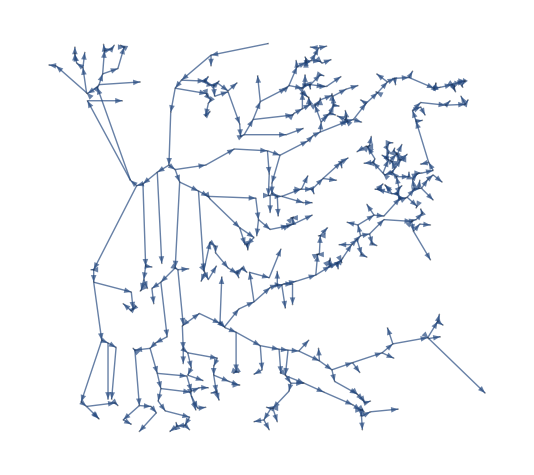
```mathematica
tree = -Graphics-;
```

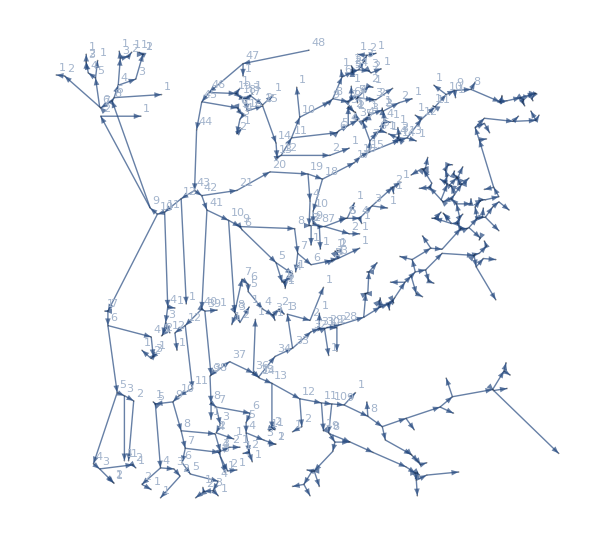

```mathematica
IGVertexMap[#&, VertexLabels->IGStrahlerNumber, %]
```

## Statistical Analysis

Statistical Analysis Code

```mathematica
levels=Select[Flatten[Drop[ExampleData[{"Statistics","LakeMeadLevels"}],None,1]],Positive];
```

```mathematica
maxLevel = 1229;
```

```mathematica
relativeLevels = levels/maxLevel;
```

```mathematica
edist=EstimatedDistribution[relativeLevels,KumaraswamyDistribution[α,β]]
```

KumaraswamyDistribution[30.543,2.7868]

```mathematica
KumaraswamyDistribution[30.54299350888491,2.7867956521488817]
```

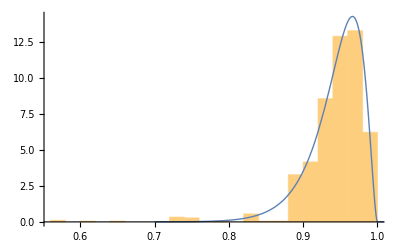

```mathematica
Show[Histogram[relativeLevels,Automatic,"PDF"],Plot[PDF[edist,x],{x,0.7,1.1},PlotStyle->Thick]]
```

```mathematica
drought=1125;
```

```mathematica
Probability[x*maxLevel<drought,x\[Distributed]edist]*100
```

```mathematica
N[Probability[x*maxLevel<drought,x\[Distributed]edist]]*100
```

```mathematica
maxLevel Mean[edist]
```

1160.59

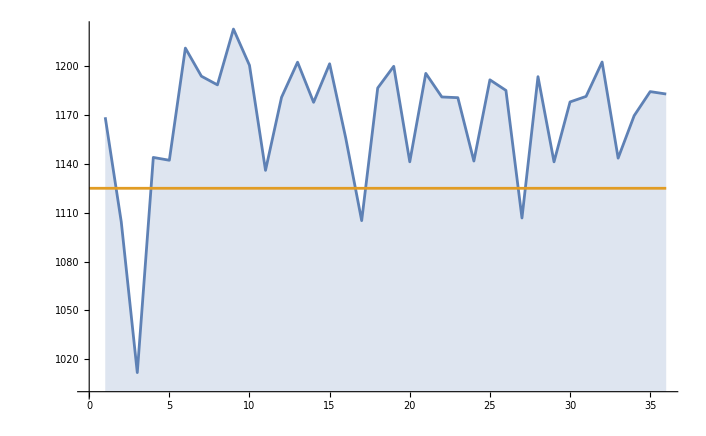

```mathematica
ListPlot[{maxLevel RandomVariate[edist,36],{{0,drought},{36,drought}}},Filling->{1->Axis},Joined->{True,True}]
```

```mathematica
data=ExampleData[{"Statistics","MahanadiRiverFlow"}]
```

{2.78,2.47,1.64,3.91,1.95,1.61,2.72,3.48,0.85,2.29,1.72,2.41,1.84,2.52,4.45,1.93,5.32,2.55,1.36,1.47,1.02,1.73}

```mathematica
mean=Mean[data];
data0=data-mean;
```

```mathematica
eproc=EstimatedProcess[data0,FARIMAProcess[4,3]]
```

EstimatedProcess[{0.415455,0.105455,-0.724545,1.54545,-0.414545,-0.754545,0.355455,1.11545,-1.51455,-0.0745455,-0.644545,0.0454545,-0.524545,0.155455,2.08545,-0.434545,2.95545,0.185455,-1.00455,-0.894545,-1.34455,-0.634545},FARIMAProcess[4,3]]

## Watershed Delineation

Watershed delineation refers to the process of identifying the boundary of a water-basin, drainage basin or
catchment. It is an extremely important process in the fields of environment science and hydrology.We start by taking
the Magnitude of the elevation of Sundarbans National Park, a famous delta basin system in India and Bangladesh.
Then, we use the ReliefPlot functionality to generate a relief plot from the array of height values.

```mathematica
data= N[QuantityMagnitude[GeoElevationData[]]];
```

```mathematica
reliefmap=ReliefPlot[data,DataReversed->True,PlotLegends->BarLegend[Automatic,LegendLabel->"elevation(m)"]]
```

-Graphics-

Next, we create an image using the array of geo-elevation values, and use the ImageAdjust function - which adjusts
the levels in image, rescaling them to account for bad lighting.

```mathematica
mimg = ImageAdjust[Image[data]]
```

-Graphics-

```mathematica
wsc=WatershedComponents[mimg,Method->"Immersion"];
```

The watershed components functionality returns the transform of an image, computes the watershed transform of
image, and returns the result as an array in which positive integers label the catchment basins. We then create an image
on the basis of the watershed components, and then apply color negate to the image to create a binary image. This
allows us to clearly see the de-segmentation of the basis into sub-basins, which is very useful.

```mathematica
bnds=ColorNegate[Image[wsc,"Bit"]]
```

-Graphics-

```mathematica
BinaryImageQ@%
```

True

Next, we apply functions such as Erosion and Dilation to obtain data about the image, and then create an association
thread between the two datasets. We then create a function to evaluate the components of the image that are minimum
and at the border of the image, and weed them out.

```mathematica
bindex=Erosion[Replace[wsc,0->Max[wsc]+1,{2}],1]
```

```mathematica
tindex = Dilation[wsc,1]
```

```mathematica
doubleIndexArray=Replace[Transpose[{bindex,tindex},{3,1,2}],{n_,n_}->{0,0},{2}]
```

```mathematica
{data, mimg, wsc, bnds, bindex, tindex, doubleIndexArray, doubleIndexPairs, bndSegs, MinATborders,g0,g1,basinConnect}= {0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
funcDelineate[region_]:=Module[{}, 
data= N[QuantityMagnitude[GeoElevationData[SemanticInterpretation[region]]]];
mimg = ImageAdjust[Image[data]];
wsc=WatershedComponents[mimg,Method->"Immersion"];
bnds=ColorNegate@Image[wsc,"Bit"];
bindex=Erosion[Replace[wsc,0->Max[wsc]+1,{2}],1];
tindex=Dilation[wsc,1];
doubleIndexArray=Replace[Transpose[{bindex,tindex},{3,1,2}],{n_,n_}->{0,0},{2}];
doubleIndexPairs=Prepend[DeleteCases[DeleteDuplicates[Flatten[doubleIndexArray,1]],{0,0}],{0,0}];
bndSegs=Replace[doubleIndexArray,Dispatch[MapIndexed[#1->First[#2]-1&,doubleIndexPairs]],{2}];
MinATborders=Thread[Rest[doubleIndexPairs]->ComponentMeasurements[{mimg,bndSegs},"Min"][[All,2]]];
g0=Graph[Apply[UndirectedEdge,Rest@doubleIndexPairs,{1}]];
g1=WeaklyConnectedGraphComponents[g0][[1]];
basinConnect=Sort[Map[#->AdjacencyList[g1,#]&,VertexList[g1]]];

Print[GraphPlot3D[g1]]
]
```

The interaction between various basin components, such as how water flows between them, is known as the hydrological connectedness of a river basin. A graph can be used to illustrate this connectivity, with each vertex representing a section of the basin and the edges denoting the links among them.
In this context, clusters are collections of linked vertices that constitute functional units in the hydrographical ecology
of the river basin. These groups represent bigger river basins or regions within it that have comparable hydrological
properties

```mathematica
funcDelineate["Sunderbans National Park"]
```

-Graphics3D-

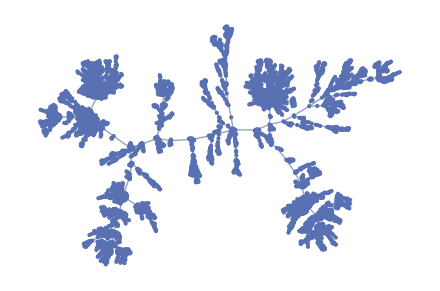

```mathematica
TransitiveReductionGraph[%47]
```

```mathematica
polygonComponents[x_]:=ColorNegate[Binarize[Graphics[Select[Cases[GeoGraphics[GeoBoundingBox[SemanticInterpretation[x]],GeoBackground->"VectorMinimal"],{Directive[{___,RGBColor[0.6,0.807843137254902,1.],___}],___},Infinity],Not@*FreeQ[Polygon]]]]]
```

```mathematica
polygonComponents["Sunderbans National Park"]
```

-Graphics-

```mathematica
DeleteBorderComponents[DeleteSmallComponents[Dilation[%711,2]]]
```

-Graphics-

Some more code for Basin Delineation

```mathematica
f[x_Image]:=FixedPoint[Module[{m,i1,m1},m=SelectComponents[#,"EmbeddedComponents",Length[#]===0&];
i1=FillingTransform[#,Dilation[m,1]];
m1=SelectComponents[ColorNegate[i1],"EmbeddedComponents",Length[#]===0&];
FillingTransform[i1,Dilation[m1,1]]]&,Binarize[x]]

i=%936[[1]]
{{i,f@i}}//Grid
```

-Graphics-

```mathematica
MorphologicalGraph[-Graphics-];
```

```mathematica
HighlightGraph[%32,Table[%47[[i]], {i,1,50}]]
```

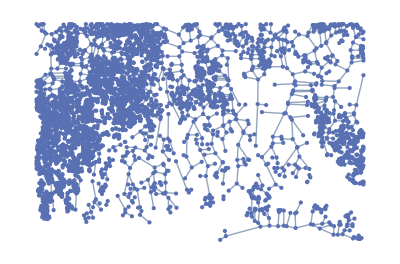
```mathematica
Subgraph[-Graphics-,KCoreComponents[-Graphics-,1],VertexShapeFunction->"Name"]
```

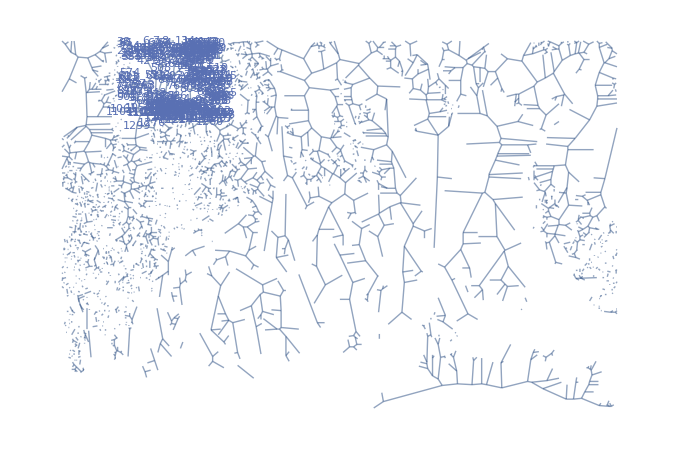

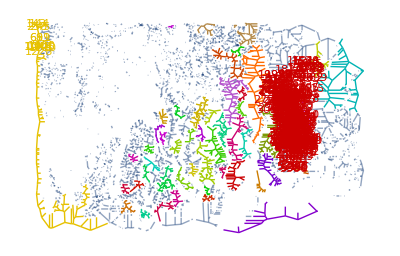

```mathematica
GraphPlot@%
```

Finally, leads to accurate watershed delineation

```mathematica
-Graphics--Graphics-
```

## Weighted Cellular Automata Model

Now, we will use a more complex cellular automata model to display the water flow. This model, called WCA2D, Weighted Cellular Automata 2D, uses a weight computing system and physical limitations to model water flow without too complex mathematical equations and fluid dynamics concepts (Guidolin et al., 2016).

In the model, the ratios of water are transferred from the central cell to the downstream neighbor cells using a weight-based system.

The water transferred will be limited by Manning’s formula and the critical flow equation, to produce a more accurate prediction of resulting water levels.

#### Collecting Data

```mathematica
elevationdata=GeoElevationData[,GeoRange->Quantity[100,"Meters"],GeoProjection->Automatic];
elevationdata=Flatten[QuantityMagnitude[Normal[elevationdata]]];
elevationdata=elevationdata-Min[elevationdata];
```

Each coordinate point, with a corresponding elevation, constitutes a cell:

```mathematica
graph = GridGraph[{7,7}];
```

The area of a cell is defined by the area of region/number of cells:

```mathematica
area=100/Length[elevationdata];
```

```mathematica
edgelength=Sqrt[area];
```

A small tolerance to set to help reduce oscillation. Downstream cells whose water levels are within tolerance of the center cell will be ignored, and won’t receive water.

Define tolerance:

```mathematica
tolerance=0.1;
```

Sets initial waterdepth to 5 at every cell(e.g. 5 in of rainfall)

```mathematica
waterdepth=Table[5,49];
```

Note that in our model, 5 represents 5ft. Although not realistic, it proves easier to visualize.

#### Algorithm

To distribute the volume being transferred from the central cell to the neighborhood,  we use a weighting system. 
1) Identify downstream cells
2) Compute weights based on available storage volume
3) Compute total volume leaving central cell
4) For each downstream cell, calculate the new intercellular-volume

We use the following helper functions to accomplish this:

#### Identifying Downstream Cells

Finds the difference in water level(elevation+waterdepth) between center and ith neighbor:

```mathematica
waterleveldiff[center_,i_] := (elevationdata[[center]] + waterdepth[[center]]) - (elevationdata[[i]] + waterdepth[[i]])
```

Available storage volume is the possible volume a neighbor cell can store from the center cell. Note that this value will be 0 for upstream cells since neighbor cells never give water. It is the water level difference, which is in m, multiplied by area (m^2).

Note that if there are no eligible cells to receive water(either upstream or doesn’t satisfy tolerance), this value is set to 0.

Finds available storage volume of the ith neighbor cell of center:

```mathematica
availstoragevol[center_,i_]:=Max[waterleveldiff[center,i],0]*area
```

Determines whether a center cells has downstream cells:

```mathematica
upstream[center_]:=If[Select[neighbors[center],waterleveldiff[center,#]>tolerance&]=={},True,False]
```

### Weight Computing

#### Helper Functions

Finds the minimum available storage volume between all the neighbor cells of a center cell:

```mathematica
minstoragevol[center_]:=area*With[{list=Select[waterleveldiff[center,#]
	&/@neighbors[center],#>tolerance&]},
	If[list=={},0,Min[list]]]
```

Finds the maximum available storage volume(used later but not in weights):

```mathematica
maxstoragevol[center_]:=area*With[{list=Select[waterleveldiff[center,#]
	&/@neighbors[center],#>tolerance&]},
	If[list=={},0,Max[list]]]
```

Finds the index of the cell with maximum available storage volume:

```mathematica
Mcell[center_]:=neighbors[center][[Position[availstoragevol[center,#]&/@neighbors[center],maxstoragevol[center]][[1,1]]]]
```

Finds the total volume that all the neighbor cells can receive from the center cell:

```mathematica
totstoragevol[center_]:=Total[availstoragevol[center,#]&/@neighbors[center]]
```

We use these functions to compute weights for the neighborhood, using the following equation:

The weight of a downstream cell is the ratio between its available storage volume and the total available storage volume, representing a fraction of the volume that the center cell will give away. To reduce oscillations, we allow the center cell to retain a fraction of the volume transferred, giving it the same weight as the minimum storage volume. The weights should always add to 1.

```mathematica
weight[center_,i_]:=availstoragevol[center,i]/(totstoragevol[center]+minstoragevol[center])
weight[center_] := minstoragevol[center]/(minstoragevol[center]+totstoragevol[center])
```

### Total Intercellular-Volume

The total intercellular-volume is the volume of water that leaves the center cell. Note that it is different from the total available storage volume previous calculated.

This value is calculated by taking the minimum of three values.

In the first term, the total intercellular-volume is limited by the amount of water that exists in the center cell.

In the second term, we use Manning’s formula and the critical flow equation that imposes a physically based equation. This dictates the maximum permissible velocity of water.

In the third term, the total intercellular-volume is limited by the minimum available storage volume  + the total intercellular-volume that left the cell in the previous time step to reduce oscillations.

Time

In our model, we treat each iteration as one time step.

#### Helper Functions

Second Term:

Finds the limiting velocity using the critical flow equation:

```mathematica
vcrt[center_] :=If[waterdepth[[center]]<=0,Sqrt[waterdepth[[center]]*9.8],Sqrt[waterdepth[[center]]*9.8]]
```

Note that we ignore Manning’s roughness coefficient since the model is carried out a variety of surfaces.

Finds the limiting velocity using Manning’s formula.

```mathematica
vman[center_]:=Power[waterdepth[[center]],(2/3)]*Sqrt[waterleveldiff[center,Mcell[center]]/edgelength]
```

Finds limiting volume based on the minimum of the two limiting velocities:

```mathematica
maxicvol[center_]:=Min[vcrt[center],vman[center]]*waterdepth[[center]]*edgelength
```

Third Term

To find the total intercellular-volume(Itot) from the previous iteration, we store the values in a new list called Itots.

```mathematica
Itots=Table[Table[0,1],49];
```

Adds the iteration to the list of Itots:

```mathematica
append[center_,time_]:={If[upstream[center]==False,Itots[[center]]=Append[Itots[[center]],Itot[center,time]],Itots[[center]]=Append[Itots[[center]],0]]}
```

We can now compute the total intercellular-volume using the following function:

```mathematica
Itot[center_,time_]:=Min[waterdepth[[center]]*area,
	maxicvol[center]/weight[center,Mcell[center]],
	If[time==1,Infinity, minstoragevol[center]+Itots[[center]][[time]]]]
```

### Depth Updating

Now, we can use our weights and total intercellular-volume to update the water depths of each cell. Each neighbor cell receives their respective weight times the total volume that leaves the center cell (Itot).

```mathematica
Icell[center_,i_,time_]:=weight[center,i]*Itot[center,time]
```

```mathematica
Icell[center_,time_]:= Itot[center,time]*weight[center]
```

Since water flows simultaneously, we must update all the cells at once. One iteration constitutes every cell in the grid being the center cell once. Those calculations are all based on the starting waterdepths, and the changes are stored in a temporary variable.

We store the changes in a variable called changes.

```mathematica
changes=Table[0,49];
```

First, we define a function calculate that performs a calculation on all the cells in the grid.

```mathematica
calculate[center_,time_,changes_]:=If[
	upstream[center]==False,
	ReplacePart[changes,Join[{center->changes[[center]]- (Itot[center, time]/area)+(Icell[center,time]/area)},Table[
		x->changes[[x]]+(Icell[center, x, time]/area),
		{x, Select[neighbors[center], availstoragevol[center, #] > tolerance&]}
	]]],changes];
```

Then, we update all of the water depths at once.

```mathematica
wmupdate[time_] := {
	Table[
		
		changes = calculate[x, time,changes];append[x,time];,{x, Length[elevationdata]}
	],
	
	waterdepth=waterdepth+changes;
	changes=Table[0,Length[elevationdata]];
}
```

### Data Visualization

Resets all the variables to initial values:

We will be using BarChart3D to visualize the model again. We will also use ArrayPlot to show how the water fluctuates as time passes.

```mathematica
reset[dim_,wtrlvl_]:={Itots = Table[Table[0,1],dim^2];
changes=Table[0,dim^2];
waterdepth=Table[wtrlvl,dim^2];}
```

```mathematica
reset[7,5];
```

Atlantic City

BarChart3D:

```mathematica
ListAnimate[First/@Table[{Show[BarChart3D[Partition[elevationdata,7],style,ColorFunction->"SiennaTones",ChartElementFunction->Function[{xyz,z},{Cuboid@@Transpose@xyz}]],BarChart3D[Partition[waterdepth+elevationdata,7],style,ColorFunction->"DeepSeaColors",ChartElementFunction->Function[{xyz,z},{Opacity[.5],Cuboid@@Transpose@(0.0015223+0.999123 xyz)}]],],wmupdate[x]},{x,10}],SaveDefinitions->True]
```

Displays waterdepth in ArrayPlot:

Princeton
We will apply this model on a portion of Princeton, New Jersey. To change dimensions, we re-define graph, area, and use the function reset.

```mathematica
elevationdata=GeoElevationData[,GeoRange->Quantity[500,"Meters"],GeoProjection->Automatic];
elevationdata=Flatten[QuantityMagnitude[Normal[elevationdata]]];

elevationdata=elevationdata-Min[elevationdata];
```

```mathematica
graph=GridGraph[{36,36}];
area=500/Length[elevationdata];
```

Resets all the variables to initial values:

```mathematica
reset[dim_,wtrlvl_]:={Itots = Table[Table[0,1],dim^2];
changes=Table[0,dim^2];
waterdepth=Table[wtrlvl,dim^2];}
```

```mathematica
reset[36,5];
```

Reversed ArrayPlot of the GeoElevationData

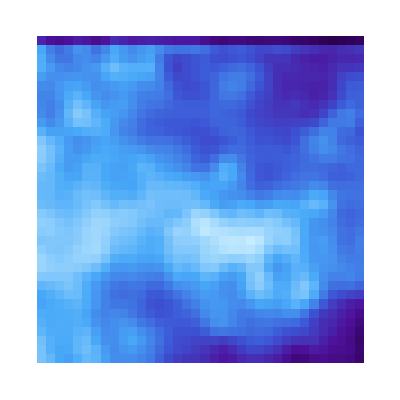

```mathematica
ArrayPlot[Partition[elevationdata,36],ColorFunction->Function[{x},ColorData["DeepSeaColors"][x]]]
```

Looking at the ArrayPlot of the water depths and the reversed ArrayPlot elevation data, we can see they look pretty similar. This means that the lower the elevation, there is generally more water. This result is similar to the Bathtub model, except there are a few differences that distinguish the two. On larger datasets, this information can be helpful for disaster mitigation.